```mathematica
Remove["Global`*"]
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[97][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[97]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

Define the expectation for a time-dependent Ornstein-Uhlenbeck process

```mathematica
Expand[( EX*Exp[(1-f)*T]-(X0)-(1-f)*Integrate[μ[t]*Exp[(1-f)*t],{t,0,T}])^2 == (1-f)^2*Integrate[Exp[2*(1-f)*t]*σ[t]^2,{t,0,T}]]
```

ⅇ^(2 (1-f) T) EX^2-2 ⅇ^((1-f) T) EX X0+X0^2-2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2==∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt

```mathematica
ESquareXFull= (∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt- (-2 ⅇ^((1-f) T) EX X0+X0^2-2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2))/ⅇ^(2 (1-f) T)
```

ⅇ^(-2 (1-f) T) (2 ⅇ^((1-f) T) EX X0-X0^2+2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt)

```mathematica
EXsol =  (X0)*Exp[-(1-f)*T]+(1-f)*Exp[-(1-f)*T]*Integrate[Exp[(1-f)*t]*μ[t],{t,0,T}]
```

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt

```mathematica
ESquareX=FullSimplify[ESquareXFull/.EX ->EXsol]
```

ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

```mathematica
SquareEX =FullSimplify[ ( EXsol)^2]
```

ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2

```mathematica
ESquareX
SquareEX
```

ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2

```mathematica
VarXFull=ESquareX-SquareEX
```

-ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

```mathematica
VarX = FullSimplify[VarXFull]
```

ⅇ^(2 (-1+f) T) (-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) ((5-5 ⅇ^(T-f T))/(1-f)+(1-ⅇ^(T-f T) (Cos[T]+(-1+f) Sin[T]))/(2+(-2+f) f))

((-1+f) (-2+ⅇ^(2 (-1+f) T)-(-2+f) f+(-1+f)^2 Cos[2 T]-(-1+f) Sin[2 T]))/(4 (2+(-2+f) f))

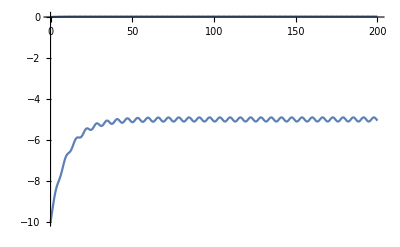

```mathematica
EXspecific = EXsol/.{μ[t]->-5+Sin[t],σ[t]->Sin[t]}
VarXSpecific=VarX/.{μ[t]->-5+Sin[t],σ[t]->Sin[t]}
Plot[{EXspecific,VarXSpecific}/.{f->0.9,X0->-10,μ0->0.5},{T,0,200}]
```

{-10 ⅇ^(-0.01 T)+0.01 ⅇ^(-0.01 T) (101.-100. ⅇ^(0.01 T)+ⅇ^(0.01 T) (-0.9999 Cos[T]+0.009999 Sin[T])),-ⅇ^(-0.02 T) (-10+0.01 (101.-100. ⅇ^(0.01 T)+ⅇ^(0.01 T) (-0.9999 Cos[T]+0.009999 Sin[T])))^2+ⅇ^(-0.02 T) ((-10+0.01 (101.-100. ⅇ^(0.01 T)+ⅇ^(0.01 T) (-0.9999 Cos[T]+0.009999 Sin[T])))^2+0.0004 (-72.9983+ⅇ^(0.02 T) (75.-1.9992 Cos[T]-0.00249975 Cos[2. T]+0.039984 Sin[T]-0.249975 Sin[2. T])))}

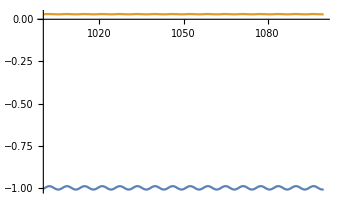

```mathematica
ExpVar = {EXspecific = EXsol,VarXSpecific=VarXFull}/.{μ[t]->-1+Sin[t],σ[t]->2+2*Sin[t],f->0.99,X0->-10,μ0->0.5}
Plot[ExpVar,{T,1000,1100}]
```

```mathematica
EXsol/.{μ[t]->-1+Sin[t],σ[t]->2*Sin[t],f->0.5,X0->-10,μ0->0.5}
```

-10 ⅇ^(-0.5 T)+0.5 ⅇ^(-0.5 T) (2.8-2. ⅇ^(0.5 T)+ⅇ^(0.5 T) (-0.8 Cos[T]+0.4 Sin[T]))

```mathematica
FullSimplify[%]
```

-1.-8.6 ⅇ^(-0.5 T)-0.4 Cos[T]+0.2 Sin[T]

```mathematica
EXsol
VarX
```

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt

ⅇ^(2 (-1+f) T) (-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt

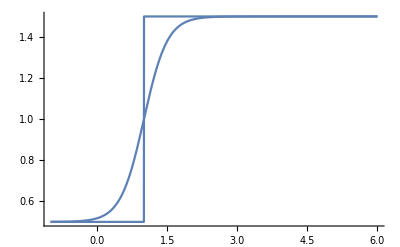

```mathematica
Show[
Plot[a1+HeavisideTheta[t-b1]/.{a1->0.5,b1->1},{t,-1,6}],
Plot[a1+1/(1+Exp[-2*k*(t-b1)])/.{k->2,a1->0.5,b1->1},{t,-1,6}]
]
```

```mathematica
EXHeavy = EXsol/.{μ[t]->a1+HeavisideTheta[t-b1],σ[t]->a2+HeavisideTheta[t-b2]}
VarXHeavy=VarX/.{μ[t]->a1+HeavisideTheta[t-b1],σ[t]->a2+HeavisideTheta[t-b2]}
EXLogistic = EXsol/.{μ[t]->a1+1/(1+Exp[-2*k*(t-b1)]),σ[t]->a2+1/(1+Exp[-2*k*(t-b2)])}
VarXLogistic=VarX/.{μ[t]->a1+1/(1+Exp[-2*k*(t-b1)]),σ[t]->a2+1/(1+Exp[-2*k*(t-b2)])}
```

ConditionalExpression[ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+1/(-1+f)ⅇ^(-f (b1+T)) (-(ⅇ^(b1 f+T)-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])))),T∈Reals]

ConditionalExpression[1/2 ⅇ^(-2 b2 (-1+f)+2 (-1+f) T) (-1+f) (a2^2 (ⅇ^(2 b2 (-1+f))-ⅇ^(2 (-1+f) (b2-T)))-(1+2 a2) (-1+ⅇ^(2 (-1+f) (b2-T))) HeavisideTheta[T] HeavisideTheta[-b2+T]+(1+2 a2) HeavisideTheta[-b2] ((-1+ⅇ^(2 b2 (-1+f))) HeavisideTheta[T] HeavisideTheta[-b2+T]+HeavisideTheta[-T] (-1+ⅇ^(2 b2 (-1+f))-(-1+ⅇ^(2 (-1+f) (b2-T))) HeavisideTheta[-b2+T]))),T∈Reals]

ConditionalExpression[ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)-(-1+Hypergeometric2F1[1,-(-1+f)/(2 k),(1-f+2 k)/(2 k),-ⅇ^(-2 b1 k)])/(-1+f)+(ⅇ^(T-f T) (-1+Hypergeometric2F1[1,-(-1+f)/(2 k),(1-f+2 k)/(2 k),-ⅇ^(2 k (-b1+T))]))/(-1+f)),ⅇ^(-2 b1 k)≥-1&&ⅇ^(2 k (-b1+T))≥-1]

$Aborted

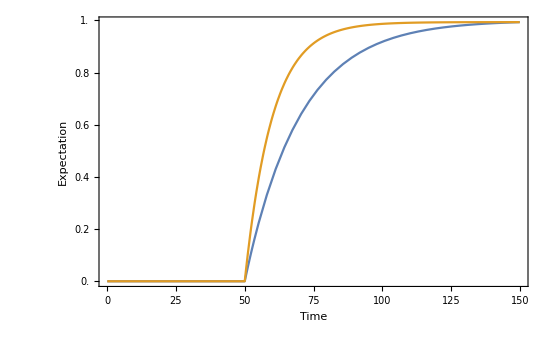

```mathematica
Show[
TwoAxisPlot[{EXHeavy,VarXHeavy}/.{f->0.95,X0->0,a1->0,b1->50,a2->0,b2->50},{T,0,150}],FrameLabel->{"Time","Expectation","","Variance"}]
```

```mathematica
D[ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+1/(-1+f)ⅇ^(-f (b1+T)) (-(ⅇ^(b1 f+T)-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])))),T]
```

ⅇ^((-1+f) T) (-1+f) X0+ⅇ^((-1+f) T) (1-f) (-1+f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+1/(-1+f)ⅇ^(-f (b1+T)) ((-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T]))))+ⅇ^((-1+f) T) (1-f) (a1 ⅇ^(T-f T)-1/(-1+f)ⅇ^(-f (b1+T)) f ((-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])))+1/(-1+f)ⅇ^(-f (b1+T)) ((-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) DiracDelta[-b1+T] HeavisideTheta[T]+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) DiracDelta[T] HeavisideTheta[-b1+T]+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T) f) HeavisideTheta[T] HeavisideTheta[-b1+T]+HeavisideTheta[-b1] ((ⅇ^(f (b1+T))-ⅇ^(b1+f T)) DiracDelta[-b1+T] HeavisideTheta[T]+(ⅇ^(f (b1+T))-ⅇ^(b1+f T)) DiracDelta[T] HeavisideTheta[-b1+T]+(ⅇ^(f (b1+T)) f-ⅇ^(b1+f T) f) HeavisideTheta[T] HeavisideTheta[-b1+T]-DiracDelta[T] (ⅇ^(f (b1+T))-ⅇ^(b1+f T)+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) HeavisideTheta[-b1+T])+HeavisideTheta[-T] (ⅇ^(f (b1+T)) f-ⅇ^(b1+f T) f+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T)) DiracDelta[-b1+T]+(-ⅇ^(b1 f+T)+ⅇ^(b1+f T) f) HeavisideTheta[-b1+T]))))

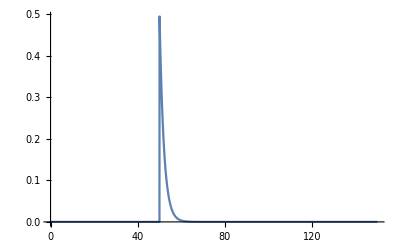

```mathematica
Plot[%218/.{X0->0,a1->0,b1->50,f->0.5},{T,0,150},PlotRange->All]
```

```mathematica
NSolve[D[EXHeavy,T]==0/.{X0->0,a1->0,b1->50,f->0.5},T]
```

NSolve[ConditionalExpression[0.-0.25 ⅇ^(-0.5 T) (0.+2. ⅇ^(-0.5 (50+T)) (-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) HeavisideTheta[-50+T] HeavisideTheta[T])+0.5 ⅇ^(-0.5 T) (-1. ⅇ^(-0.5 (50+T)) (-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) HeavisideTheta[-50+T] HeavisideTheta[T]-2. ⅇ^(-0.5 (50+T)) (-(-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) DiracDelta[T] HeavisideTheta[-50+T]-(-ⅇ^(50+0.5 T)+ⅇ^(25.+T)) DiracDelta[-50+T] HeavisideTheta[T]-(-0.5 ⅇ^(50+0.5 T)+ⅇ^(25.+T)) HeavisideTheta[-50+T] HeavisideTheta[T]))==0,T∈Reals],T]

```mathematica
EXSin = EXsol/.{μ[t]->a1+b1*Sin[ω1*t],σ[t]->a2+b2*Sin[ω2*t]}
VarXSin=VarX/.{μ[t]->a1+b1*Sin[ω1*t],σ[t]->a2+b2*Sin[ω2*t]}
```

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) (-(a1-a1 ⅇ^(T-f T))/(1-f)+(ⅇ^(-f T) (b1 ⅇ^(f T) ω1-b1 ⅇ^T (ω1 Cos[T ω1]+(-1+f) Sin[T ω1])))/((-1+f)^2+ω1^2))

1/4 ⅇ^(2 (-1+f) T) (-1+f)^2 ((2 a2^2+b2^2)/(-1+f)-(b2^2 (-1+f))/(1-2 f+f^2+ω2^2)+(8 a2 b2 ω2)/(4-8 f+4 f^2+ω2^2)+ⅇ^(-2 (-1+f) T) ((2 a2^2+b2^2)/(1-f)-(8 a2 b2 ω2 Cos[T ω2])/(4-8 f+4 f^2+ω2^2)+(b2^2 (-1+f) Cos[2 T ω2])/(1-2 f+f^2+ω2^2)-(16 a2 b2 (-1+f) Sin[T ω2])/(4-8 f+4 f^2+ω2^2)-(b2^2 ω2 Sin[2 T ω2])/(1-2 f+f^2+ω2^2)))

```mathematica
FullSimplify[EXSin]
FullSimplify[VarXSin]
```

ⅇ^((-1+f) T) (X0+(ⅇ^(-f T) (-b1 ⅇ^(f T) (-1+f) ω1+a1 (ⅇ^T-ⅇ^(f T)) ((-1+f)^2+ω1^2)+b1 ⅇ^T (-1+f) (ω1 Cos[T ω1]+(-1+f) Sin[T ω1])))/((-1+f)^2+ω1^2))

1/4 ⅇ^(2 (-1+f) T) (-1+f)^2 ((2 a2^2+b2^2)/(-1+f)-(b2^2 (-1+f))/((-1+f)^2+ω2^2)+(8 a2 b2 ω2)/(4 (-1+f)^2+ω2^2)+ⅇ^(-2 (-1+f) T) ((2 a2^2+b2^2)/(1-f)-(8 a2 b2 ω2 Cos[T ω2])/(4 (-1+f)^2+ω2^2)+(b2^2 (-1+f) Cos[2 T ω2])/((-1+f)^2+ω2^2)-(16 a2 b2 (-1+f) Sin[T ω2])/(4 (-1+f)^2+ω2^2)-(b2^2 ω2 Sin[2 T ω2])/((-1+f)^2+ω2^2)))

```mathematica
EXSinStationary = FullSimplify[a1+(-b1*(1-f) *(ω1 Cos[T ω1]+(-1+f) Sin[T ω1]))/((-1+f)^2+ω1^2)]
VarXSinStationary=FullSimplify[1/4 (-1+f)^2((2 a2^2+b2^2)/(1-f)-(8 a2 b2 ω2 Cos[T ω2])/(4 (-1+f)^2+ω2^2)+(b2^2 (-1+f) Cos[2 T ω2])/((-1+f)^2+ω2^2)-(16 a2 b2 (-1+f) Sin[T ω2])/(4 (-1+f)^2+ω2^2)-(b2^2 ω2 Sin[2 T ω2])/((-1+f)^2+ω2^2))]
```

a1+(b1 (-1+f) (ω1 Cos[T ω1]+(-1+f) Sin[T ω1]))/((-1+f)^2+ω1^2)

1/4 (-1+f)^2 ((2 a2^2+b2^2)/(1-f)-(8 a2 b2 ω2 Cos[T ω2])/(4 (-1+f)^2+ω2^2)+(b2^2 (-1+f) Cos[2 T ω2])/((-1+f)^2+ω2^2)-(16 a2 b2 (-1+f) Sin[T ω2])/(4 (-1+f)^2+ω2^2)-(b2^2 ω2 Sin[2 T ω2])/((-1+f)^2+ω2^2))

```mathematica
Manipulate[
Plot[{EXSin,EXSinStationary,
a1+b1*Sin[ω1*T]}/.{a1->1,b1->0.5,X0->-10,f->F,ω1->Omega1},{T,5500,5550},PlotRange->{-1,3}],
{F,0,0.99},{Omega1,0,2Pi}]
```

```mathematica
Manipulate[
Plot[{EXSin}/.{a1->1,b1->1,X0->-10,f->F,ω1->Omega1},{T,90,100},PlotRange->{-1,3}],
{F,0.0001,0.99},{Omega1,0,2Pi}]
```

```mathematica
(-b1*(1-f)*w1)^2
```

b1^2 (1-f)^2 w1^2

```mathematica
FullSimplify[Sqrt[b1^2*(1+(1-f)^2 w1^2)]]
```

√(b1^2 (1+(-1+f)^2 w1^2))

```mathematica
FullSimplify[(√(b1^2 (1+(-1+f)^2 w1^2)))/((f-1)^2+w1^2)]
```

(√(b1^2 (1+(-1+f)^2 w1^2)))/((-1+f)^2+w1^2)